```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of March 22, 2011, 21:10:4.67737.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
rule = {X[a_** b_]** X[c_ ]:> X[X[a **c]**X[b **c]]};
Dash[t_]:= Simplify[(t)/.rule]
```

```mathematica
Flog = X[x ** y] ** X[z]
Dash[Flog]
Dash[Dash[Flog]]
Dash[Dash[Dash[Flog]]]
Dash[Dash[Dash[Dash[Flog]]]]
```

X[x**y]**X[z]

X[X[x**z]**X[y**z]]

X[X[X[x**y**z]**X[z**y**z]]]

X[X[X[X[x**z**y**z]**X[y**z**z**y**z]]]]

X[X[X[X[X[x**y**z**z**y**z]**X[z**y**z**y**z**z**y**z]]]]]

```mathematica
Flog = X[x ** x] ** X[x]
Dash[Flog]
Dash[Dash[Flog]]
Dash[Dash[Dash[Flog]]]
Dash[Dash[Dash[Dash[Flog]]]]
```

X[x**x]**X[x]

X[X[x**x]**X[x**x]]

X[X[X[x**x**x]**X[x**x**x]]]

X[X[X[X[x**x**x**x]**X[x**x**x**x**x]]]]

X[X[X[X[X[x**x**x**x**x**x]**X[x**x**x**x**x**x**x**x]]]]]

```mathematica
Flog = X[x ** y] ** X[z]
Dash[Dash[Dash[Dash[Dash[Flog]]]]]
Dash[Dash[Dash[Dash[Dash[Dash[Flog]]]]]]
Dash[Dash[Dash[Dash[Dash[Dash[Dash[Flog]]]]]]]
Dash[Dash[Dash[Dash[Dash[Dash[Dash[Dash[Flog]]]]]]]]
```

X[x**y]**X[z]

X[X[X[X[X[X[x**z**y**z**y**z**z**y**z]**X[y**z**z**y**z**z**y**z**y**z**z**y**z]]]]]]

X[X[X[X[X[X[X[x**y**z**z**y**z**z**y**z**y**z**z**y**z]**X[z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z]]]]]]]

X[X[X[X[X[X[X[X[x**z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z]**X[y**z**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z]]]]]]]]

X[X[X[X[X[X[X[X[X[x**y**z**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z]**X[z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z**y**z**z**y**z**z**y**z**y**z**z**y**z]]]]]]]]]

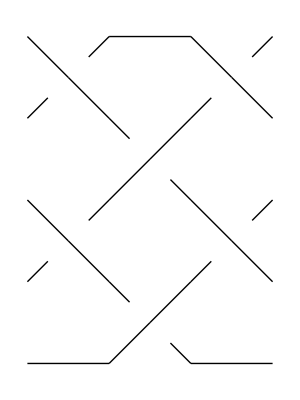

```mathematica
br=BR[5,{{1,3},{-2,-4},{1,3}}];
Show[BraidPlot[br]]
```